# Tutorial 7: 1D Oscillator in the Configuration Plane

PHYS1110D Tutorial Class - October 15, 2019

by YUE Zhengyuan

Oscillators with equation of motion

m (ⅆ^2 x)/(ⅆ t^2)(t)=-k x^2

is an important model system in many branches of physics: in classical mechanics, it is the best introduction to differential equations; in quantum mechanics and statistical physics, it ultimately leads to the concept of quantum fields and quasi-particles. Therefore, it is worthwhile to give this subject a detailed treatment in any introductory physics courses.

There are many variants of the oscillator model. For example, we can introduce an air resistance:

m (ⅆ^2 x)/(ⅆ t^2)=-k x-α ⅆx/ⅆt=-k x-α v

And we say that this oscillator is “damped”. This equation can still be solved exactly. But if more complicated forces are introduced, we will have to use numerical methods to solve for the motion case by case. In order to visualize the numerical solutions, besides the old position-velocity graph, physicists and mathematicians introduced the configuration plane (a fancy name for the x v - plane). The trajectory of the oscillator in this plane can tell us many properties of the motion that are not clearly revealed in the solution.

## 7.Section. Oscillator and Configuration Plane

First, let us consider the simplest case eq. (1.1). The mechanical energy of the object + spring system is

E=1/2 m v^2+1/2 k x^2

Suppose that the oscillator is initially at x(0)=x_0 with zero velocity (v(0)=0). The energy is then always 1/2 k x_0^2, and the trajectory of the system is in general an ellipse (may be a circle under certain conditions):

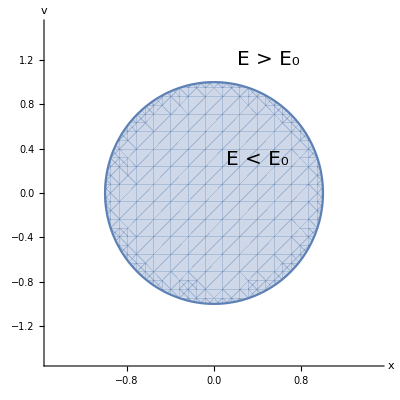

```mathematica
Clear["Global`*"]
m=1;k=1;x0=1;
fig=RegionPlot[1/2 m v^2+1/2 k x^2≤1/2 k x0^2,{x,-1.5,1.5},{v,-1.5,1.5}];
labels=Graphics[{Black,Text[Style["E > E_0",20],{0.5,1.2}],
Text[Style["E < E_0",20],{0.4,0.3}]}];
Show[fig, labels,Frame->False,Axes->True,AxesStyle->Directive[Thick,Black,20],Ticks->Automatic,AxesLabel->{x,v}]
```

The center of the ellipse is at (0,0), exactly corresponding to the equilibrium position. Then it is obvious that the equilibrium state has a lower energy than the initial state.

## 7.Section. Trajectory of a Damped Oscillator

How does the particle move on the configuration plane? Analogous to the familiar relation in real plane (x,y)

ⅆ/ⅆt(x
y)=(v_x
v_y)      (Time derivative of the coordinate is the velocity)

We have for the configuration plane (x,v)

ⅆ/ⅆt(x
v)=(v
a)

This is the “velocity” of the “motion” in the configuration plane. Now we can plot the path of the object in the configuration plane numerically. Taking a small time step τ, and assuming that the object is moving with constant velocity v_n in the nth interval (this can be called as the first order approximation), we obtain

x_(n+1)-x_n=v_n τ,    v_(n+1)-v_n=a_n τ

Here x_n=x(t_n), v_n=v(t_n), etc. The acceleration is given by a_n=1/m(-k x_n-α v_n).

Starting from the initial values

x(t_0)=x_0, v(t_0)=0     (t_0=0)

We can find the trajectory of the object in the configuration plane. First let’s verify that the trajectory is just the ellipse when the air resistance is absent (α=0)

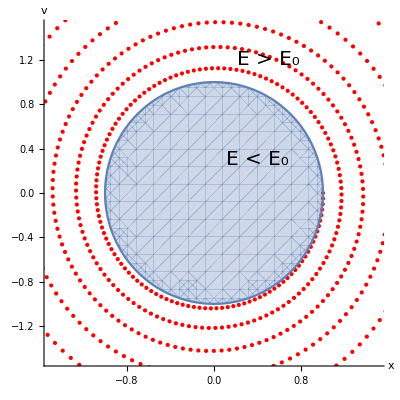

```mathematica
α=0;τ=0.05;
totalstep=10^3;
a[x_,v_]:=1/m(-k x-α v)
pos=RecurrenceTable[{x[n+1]-x[n]==v[n]τ,v[n+1]-v[n]==a[x[n],v[n]]τ,x[0]==x0,v[0]==0},{x,v},{n,0,totalstep}];
points=Graphics[{Red,Point[pos]}];
Show[points,fig,labels,PlotRange->{{-1.5,1.5},{-1.5,1.5}},Frame->False,Axes->True,AxesStyle->Directive[Thick,Black,20],Ticks->Automatic,AxesLabel->{x,v}]
```

However, we see that our naive algorithm will eventually increase the system energy (the trajectory goes outside the ellipse). To overcome this problem, people suppose instead that the object is moving with velocity v_(n+1/2) (i.e. the velocity at time t_n+τ/2). This method is called the leapfrog algorithm:

x_(n+1)-x_n=v_(n+1/2) τ,      v_(n+1/2)-v_(n-1/2)=a_n τ

It can be converted to equations defined only on integral time t_n :

x_(n+1)-x_n=v_n τ+1/2 a_n τ^2,      v_(n+1)-v_n=(a_(n+1)+a_n)/2 τ

Conversion: 	For the first equation

v_(n+1/2)=v_n+1/2 a_n τ ⇒x_(n+1)-x_n=(v_n+1/2 a_n τ)  τ=v_n τ+1/2 a_n τ^2

For the second equation

v_(n+1)=v_(n+1/2)+1/2 a_(n+1)τ , v_n=v_(n+1/2)-1/2 a_n τ⇒v_(n+1)-v_n=(v_(n+1/2)+1/2 a_(n+1)τ )-(v_(n+1/2)-1/2 a_n τ)=(a_(n+1)+a_n)/2 τ

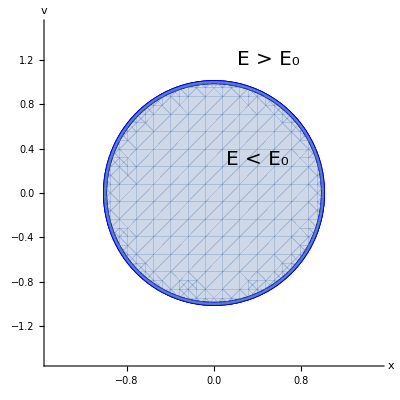

```mathematica
pos2=RecurrenceTable[{
x[n+1]-x[n]==v[n]τ+1/2 a[x[n],v[n]] τ^2,
v[n+1]-v[n]==1/2(a[x[n+1],v[n+1]]+a[x[n],v[n]])τ,x[0]==x0,v[0]==0},{x,v},{n,0,totalstep}];
points2=Graphics[{Blue,Point[pos2]}];
Show[points2,fig,labels,PlotRange->{{-1.5,1.5},{-1.5,1.5}},Frame->False,Axes->True,AxesStyle->Directive[Thick,Black,20],Ticks->Automatic,AxesLabel->{x,v}]
```

This is much better. Now we turn on the air resistance and use the leapfrog algorithm to calculate the trajectory:

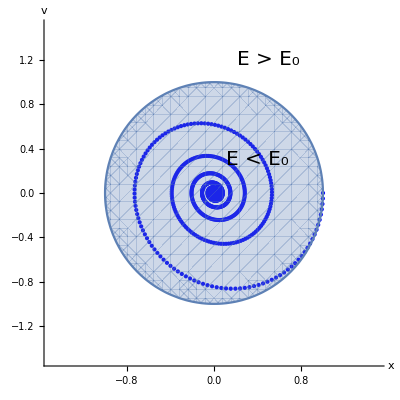

```mathematica
α=0.2;
pos2=RecurrenceTable[{
x[n+1]-x[n]==v[n]τ+1/2 a[x[n],v[n]] τ^2,
v[n+1]-v[n]==1/2(a[x[n+1],v[n+1]]+a[x[n],v[n]])τ,x[0]==1,v[0]==0},{x,v},{n,0,totalstep}];
points2=Graphics[{Blue,Point[pos2]}];
Show[points2,fig,labels,PlotRange->{{-1.5,1.5},{-1.5,1.5}},Frame->False,Axes->True,AxesStyle->Directive[Thick,Black,20],Ticks->Automatic,AxesLabel->{x,v}]
```

We see that the trajectory is “attracted” to the center of the ellipse (the equilibrium position), as we expected.

## 7.Section. The Analytical Solution for Damped Oscillators

It turns out that the motion of a damped oscillator can be solved analytically. How? The trick is to make use of the exponential function. You know that this function has a very nice property:

ⅆ/ⅆx ⅇ^(a x)=a ⅇ^(a x)     (a∈ℂ)

i.e. the differentiation is converted to multiplication. We emphasize that this is true for all complex numbers a.

You might wonder: what is ⅇ^(ⅈ α) (α∈ℝ)? The result is a very famous equality in mathematics:

ⅇ^(ⅈ α)=cos α+ⅈ sin α    (α∈ℝ)

You can prove it using the Taylor series of the exponential, the sine, and the cosine functions. Now, for the damped oscillator

m (ⅆ^2 x)/(ⅆ t^2)=-k x-α ⅆx/ⅆt

We assume

x(t)=C ⅇ^(ⅈ ω t)

Then, substituting it to the equation of motion, we get

-m ω^2 C ⅇ^(ⅈ ω t)=-k C ⅇ^(ⅈ ω t)-ⅈ ω α C ⅇ^(ⅈ ω t)

We cross out the common factor x_0 ⅇ^(ⅈ ω t) to obtain an equation for ω:

m ω^2=k+ⅈ ω α

This is just an quadratic equation, which you should know how to solve since middle school. There are two solutions:

```mathematica
Clear[m,k,α]
Solve[m ω^2==k+ⅈ ω α,ω]//Simplify//TraditionalForm
```

{{ω→-(√(4 k m-α^2)-ⅈ α)/(2 m)},{ω→(√(4 k m-α^2)+ⅈ α)/(2 m)}}

Now we define

β=α/(2m), ω=(√(4k m-α^2))/(2m)

We get the general solution of the equation of motion:

x(t)=C_1 ⅇ^(ⅈ(ⅈ β+ω)t)+C_2 ⅇ^(ⅈ(ⅈ β-ω)t)=ⅇ^(-β t)(C_1 ⅇ^(ⅈ ω t)+C_2 ⅇ^(-ⅈ ω t))

The ⅇ^(-β t) factor means that the oscillation amplitude is decaying exponentially. Here we introduced two constants C_1,C_2. To determine their value, we need the initial conditions:

x(0)=x_0, v(0)=(ⅆx(0))/ⅆt=0

Besides, the solution should be real. Therefore

C_2=C_1^*

Then you can get the real and the imaginary parts of the constant C_1=A+ⅈ B:

```mathematica
Clear[x,t]
x[t_]:=Exp[-β t]((A+ⅈ B)Exp[ⅈ ω t]+(A-ⅈ B)Exp[-ⅈ ω t])//Simplify;
v[t_]:=D[x[t′],t′]/.{t′->t}//Simplify;
Solve[x[0]==x0&&v[0]==0,{A,B}]//Simplify//TraditionalForm
```

{{A→1/2,B→-β/(2 ω)}}

So we get the solution

x(t)=ⅇ^(-β t+ⅈ ω t)(x_0/2-(ⅈ β x_0)/(2ω))+ⅇ^(-β t-ⅈ ω t)(x_0/2+(ⅈ β x_0)/(2ω))

If we turn off the resistance (setting α=0), then β=0, ω=√(k/m). We recover the familiar result:

x(t;α=0)=x_0/2(ⅇ^(ⅈ ω t)+ⅇ^(-ⅈ ω t))=x_0 cos (ω t)

Comparing the exact solution and the numerical solution obtained by the leapfrog algorithm:

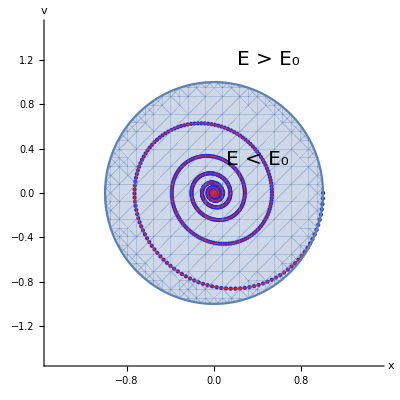

```mathematica
Clear[x];
m=1;x0=1;k=1;α=0.2;
β=α/(2m);ω=(√(4 k m-α^2))/(2m);
x[t_]:=Exp[-β t+ⅈ ω t](x0/2-(ⅈ β x0)/(2ω))+Exp[-β t-ⅈ ω t](x0/2+(ⅈ β x0)/(2ω));
curve={x[t],D[x[t],t]};
exact=ParametricPlot[curve, {t,0,totalstep*τ},PlotStyle->Directive[Thick,Red]];
Show[points2,exact,fig,labels,PlotRange->{{-1.5,1.5},{-1.5,1.5}},Frame->False,Axes->True,AxesStyle->Directive[Thick,Black,20],Ticks->Automatic,AxesLabel->{x,v}]
```

Excellent match! This means that the leapfrog algorithm is more reliable. Why? And why does the “naive” algorithm will lead to an increase in energy? We encourage you to search the Internet or go to the library to find it out by yourself.